# Schwarz-Christoffel

If I have a bunch of points on the real axis 
	A_1<A_2<…<A_(n-1)<A_n=∞
and a bunch of positive exponents β_1,β_2,…,β_n satisfying 
	1<∑_(k=1)^n β_k
and define
	S[z]=∫_0^z 1/(∏_(k=1)^(n-1) (ζ-A_k)^β_k)dζ

Lets see what happens with A_(1:3)={0,1,∞} and β_(1:3)={0.5,0.5,0}

1/((-1.+ζ)^0.5 (0.+ζ)^0.5)

-2. Log[√(-1.+ζ)-1. √ζ]

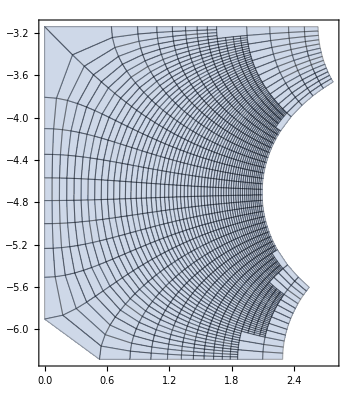

```mathematica
A={0.0,1.0,∞};
β={0.5,0.5,0};
n=Length[β];
SCIntegrand=Product[(ζ-A⟦i⟧)^(-β⟦i⟧),{i,1,n-1}]
SC[ζ_]=Integrate[SCIntegrand,ζ]

ParametricPlot[ReIm[SC[x+I y]],{x,-3,3},{y,0,2},
Mesh->All]
```